```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-SMQCD-NLO_FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
```

## g- t- t (1-loop)

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →3, with {} →{-F[9],F[9],V[4]} and all the momenta set as outgoing ({} → {p1,p2,p3}).
However the choice below produces nicer diagrams.

generic model {Lorentz} initialized

classes model {../../FA_models/SMS-stop-SMQCD-NLO_FA} initialized

in total: 6 Particles insertions

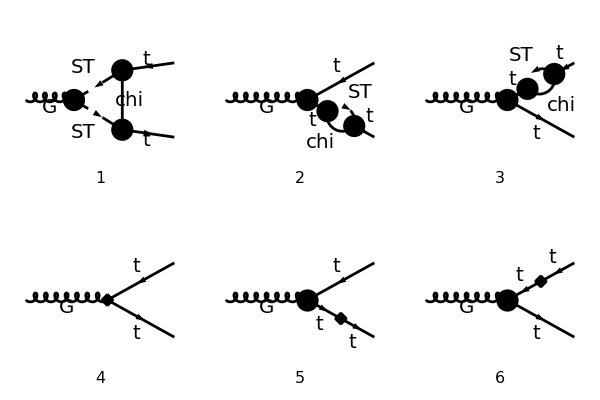

```mathematica
topsCT = CreateCTTopologies[1,1->2];
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
processGGT =  {V[1]}->  {-F[3],F[3]};
allDiags = InsertFields[Join[tops,topsCT],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],V[2],V[3]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{3,2},ImageSize->{ 600,400},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p3},OutgoingMomenta->{-p1,-p2},LoopMomenta->{q},List->False,SUNIndexNames->{cc3,aa,bb},SUNFIndexNames->{a,c1,c2},DropSumOver->True,LorentzIndexNames->{ μ}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,FR$deltaZ[{G,G},{{}}]->deltaZG,FR$deltaZ[{t,t},{{}},"L"]->deltaZL,FR$deltaZ[{t,t},{{}},"R"]->deltaZR,FR$delta[{MT},{}]->deltaM,FR$delta[{aS},{}]->deltaaS};
ampB =FullSimplify[SUNSimplify[DiracSimplify[FCReplaceMomenta[ampA,{p3->-p1-p2}]]]];
```

in total: 6 Particles amplitudes

Simplify counter-terms (see top_SelfEnergy_CT.nb and top-Vertex_CT.nb):

```mathematica
CTsubs={deltaZG->0,deltaaS->0,deltaZL -> Pi^2yDM^2  MT^2  Re[DB1[MT^2,mChi^2,mST^2,BReduce->False]],deltaZR-> Pi^2  yDM^2( MT^2 Re[DB1[MT^2,mChi^2,mST^2,BReduce->False]]+Re[B1[MT^2,mChi^2,mST^2,BReduce->False]]),deltaM->-Pi^2/2 yDM^2 MT B1[MT^2,mChi^2,mST^2,BReduce->False]};
ampB2=ampB/.CTsubs;
```

Evaluate Loop integrals:

```mathematica
ampC =FCCanonicalizeDummyIndices[( TID[ampB2,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True]//Simplify),LorentzIndexNames-> {μ,ν}];
```

## Off - Shell Case

```mathematica
FCClearScalarProducts[];
```

```mathematica
SPD[p1,p2]=1/2(s-SPD[p1,p1]-SPD[p2,p2]);
```

```mathematica
ampD=FullSimplify[DiracSimplify[FCReplaceMomenta[ampC,{p3->-p1-p2}]]];
```

```mathematica
(* Rewrite the A0 and B0 integrals in terms of B1 to simplify the expressions *)
(*loopRep = {B0[psq_,mChi^2,mST^2]->1/(psq+mChi^2-mST^2)(-2 psq PaVe[1,{psq},{mChi^2,mST^2}]+A0[mChi^2]-A0[mST^2])};*)
```

```mathematica
ampEsimp2=Simplify[(ExpandScalarProduct[DiracSimplify[ampD]])];
```

## Check Divergences

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,B1,DB1,PaVe}];
lIntsUV=Table[lInt->PaXEvaluateUV[lInt,PaXImplicitPrefactor->1/(2 Pi)^4],{lInt,lInts}];
(*lIntsUV=Join[lIntsUV,{deltaZL->0,deltaZR->Pi^2 yDM^2PaXEvaluateUV[B1[a,mChi^2,mST^2],PaXImplicitPrefactor->1/(2 Pi)^4],deltaM->-1/2 Pi^2 yDM^2 MT PaXEvaluateUV[B1[a,mChi^2,mST^2],PaXImplicitPrefactor->1/(2 Pi)^4]}];*)
lIntsUV//MatrixForm
```

PaXEvaluate::convFail: Warning! Not all scalar loop integrals in the expression could be prepared to be processed with Package X. Following integrals will not be handled by Package X: {DB1(MT^2,mChi^2,mST^2,BReduce→False)}

(B_1(MT^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV)
DB1(MT^2,mChi^2,mST^2,BReduce→False)→0
B_1(p1^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV)
B_1(p2^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV)
C_1(s,p1^2,p2^2,mST^2,mST^2,mChi^2)→0
C_1(s,p2^2,p1^2,mST^2,mST^2,mChi^2)→0
C_00(s,p1^2,p2^2,mST^2,mST^2,mChi^2)→1/(64 π^4 ε_UV)
C_11(s,p1^2,p2^2,mST^2,mST^2,mChi^2)→0
C_11(s,p2^2,p1^2,mST^2,mST^2,mChi^2)→0
C_12(p1^2,s,p2^2,mChi^2,mST^2,mST^2)→0)

```mathematica
loopUV=FullSimplify[ampEsimp2/.lIntsUV,Assumptions->{EpsilonUV ∈Reals}]
```

0

## Simplify Result

### Replace momenta squared

```mathematica
ampEsimp3a=Simplify[DiracSimplify[FeynAmpDenominatorExplicit[ampEsimp2]]/.{Pair[Momentum[p1,D],Momentum[p1,D]]->p1sq,Pair[Momentum[p2,D],Momentum[p2,D]]->p2sq}];
```

### Order PaVe integrals (note that B1 and DB1 are already ordered as B1[x] = B1[x,mChi^2,mST^2] and DB1[x] = DB1[x,mChi^2,mST^2])

```mathematica
lInts = Cases2[ampEsimp3a,{A0,B0,C0,B1,D0,PaVe}];
orderedPaVes=Table[lInt->PaVeOrder[lInt,PaVeOrderList->{s,p2sq,mChi^2,mST^2,mST^2},Sum->True],{lInt,lInts}];
ampEsimp4=ampEsimp3a/.orderedPaVes;
lIntsOrdered = Cases2[ampEsimp4,{A0,B0,C0,D0,B1,DB1,PaVe}];
lIntsOrdered//MatrixForm
```

(DB1(MT^2,mChi^2,mST^2,BReduce→False)
B_1(MT^2,mChi^2,mST^2)
B_1(p1sq,mChi^2,mST^2)
B_1(p2sq,mChi^2,mST^2)
C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)
C_2(p1sq,s,p2sq,mChi^2,mST^2,mST^2)
C_00(p1sq,s,p2sq,mChi^2,mST^2,mST^2)
C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2)
C_12(p1sq,s,p2sq,mChi^2,mST^2,mST^2)
C_22(p1sq,s,p2sq,mChi^2,mST^2,mST^2))

### Simplify arguments of PaVe integrals

```mathematica
massArgs={mChi^2,mST^2,mST^2};
subsPaVe={
B1[a1_,mChi^2,mST^2,__]:>B1[a1],
PaVe[1,{a1_},{mChi^2,mST^2},__]:>B1[a1],
DB1[a1_,mChi^2,mST^2,__]:>DB1[a1],
PaVe[0,0,{a1_,a2_,a3_},massArgs,__]:>C00[a1,a2,a3],
PaVe[1,1,{a1_,a2_,a3_},massArgs,__]:>C11[a1,a2,a3],
PaVe[2,2,{a1_,a2_,a3_},massArgs,__]:>C22[a1,a2,a3],
PaVe[1,2,{a1_,a2_,a3_},massArgs,__]:>C12[a1,a2,a3],
PaVe[1,{a1_,a2_,a3_},massArgs,__]:>C1[a1,a2,a3],
PaVe[2,{a1_,a2_,a3_},massArgs,__]:>C2[a1,a2,a3]};
```

```mathematica
ampEsimp5=FeynAmpDenominatorExplicit[DiracSimplify[ampEsimp4]]/.subsPaVe;
```

## Extract Tensor Structure

```mathematica
spinorChains1=Tally[Cases[{ampEsimp5},DiracGamma[___],All]][[All,1]];
spinorChains2=Tally[Cases[{ampEsimp5},DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains3=Tally[Cases[{ampEsimp5},DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
spinorChains4=Tally[Cases[{ampEsimp5},DiracGamma[___].DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]];
allTerms=Sort[Join[spinorChains1,spinorChains2,spinorChains3,spinorChains4]]
allPairs=Join[Select[Cases2[ampEsimp5,Pair],MemberQ[#,LorentzIndex[a__]]&],{1}]
su3prods=Join[Cases2[ampEsimp5,SUNTF],Cases2[ampEsimp5,SUNF]]
```

{(γ̄)^6,(γ̄)^7,γ^μ,γ·p1,γ·p2,γ^μ.(γ̄)^6,γ^μ.(γ̄)^7,γ^μ.(γ·p1),(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6,(γ·p2).γ^μ,γ^μ.(γ·p1).(γ̄)^6,γ^μ.(γ·p1).(γ̄)^7,(γ·p2).γ^μ.(γ̄)^6,(γ·p2).γ^μ.(γ̄)^7}

{p1^μ,p2^μ,1}

{T_c2c1^cc3}

```mathematica
(* Build all terms with exactly one μ index *)
allVars=Select[Flatten[KroneckerProduct[su3prods,allPairs,allTerms]],Count[#,LorentzIndex[μ,D],Infinity]==1&];
```

### Coefficients for each term

Define short names for each coefficient

```mathematica
su3Terms={};
Do[c=FullSimplify[Coefficient[Expand[ampEsimp5],allVars[[i]]]];
If[c==0,Continue[]];
c= Collect[c/(I Pi^2 gs yDM^2),{deltaS,deltaSp,deltaCTL,deltaCTR,B1F[a__]},FullSimplify];
AppendTo[su3Terms,{allVars[[i]],c}];
,{i,1,Length[allVars]}];;
```

#### Check that all terms have been correctly split

```mathematica
ampTot = I Pi^2 gs yDM^2  Sum[su3Terms[[i,1]] su3Terms[[i,2]],{i,1,Length[su3Terms]}];
Simplify[ampTot-ampEsimp5]
```

0

```mathematica
FullSimplify[su3Terms]
```

(p1^μ (γ·p1).(γ̄)^6 T_c2c1^cc3 | C1(p1sq,s,p2sq)+2 C11(p1sq,s,p2sq)
p1^μ (γ·p2).(γ̄)^6 T_c2c1^cc3 | -2 C12(p1sq,s,p2sq)-C2(p1sq,s,p2sq)
p2^μ (γ·p1).(γ̄)^6 T_c2c1^cc3 | -C1(p1sq,s,p2sq)-2 C12(p1sq,s,p2sq)
p2^μ (γ·p2).(γ̄)^6 T_c2c1^cc3 | C2(p1sq,s,p2sq)+2 C22(p1sq,s,p2sq)
γ^μ T_c2c1^cc3 | -(MT^2 (2 MT^2-p1sq-p2sq) (Re(B1(MT^2))-B1(MT^2)+2 MT^2 Re(DB1(MT^2))))/(2 (MT^2-p1sq) (MT^2-p2sq))
γ^μ.(γ̄)^6 T_c2c1^cc3 | (2 (MT^2-p1sq) (MT^2-p2sq) C00(p1sq,s,p2sq)+(MT^4-p1sq p2sq) (Re(B1(MT^2))+MT^2 Re(DB1(MT^2)))+p1sq B1(p1sq) (p2sq-MT^2)+p2sq B1(p2sq) (p1sq-MT^2))/((MT^2-p1sq) (MT^2-p2sq))
γ^μ.(γ̄)^7 T_c2c1^cc3 | (MT^2 Re(DB1(MT^2)) (MT^4-p1sq p2sq))/((MT^2-p1sq) (MT^2-p2sq))
T_c2c1^cc3 γ^μ.(γ·p1) | -(MT (Re(B1(MT^2))-B1(MT^2)+2 MT^2 Re(DB1(MT^2))))/(2 (MT^2-p1sq))
T_c2c1^cc3 (γ·p2).γ^μ | (MT (Re(B1(MT^2))-B1(MT^2)+2 MT^2 Re(DB1(MT^2))))/(2 (MT^2-p2sq))
T_c2c1^cc3 γ^μ.(γ·p1).(γ̄)^6 | (MT (Re(B1(MT^2))-B1(p1sq)+MT^2 Re(DB1(MT^2))))/(MT^2-p1sq)
T_c2c1^cc3 γ^μ.(γ·p1).(γ̄)^7 | (MT^3 Re(DB1(MT^2)))/(MT^2-p1sq)
T_c2c1^cc3 (γ·p2).γ^μ.(γ̄)^6 | (MT^3 Re(DB1(MT^2)))/(p2sq-MT^2)
T_c2c1^cc3 (γ·p2).γ^μ.(γ̄)^7 | (MT (Re(B1(MT^2))-B1(p2sq)+MT^2 Re(DB1(MT^2))))/(p2sq-MT^2))

```mathematica
su3TermsExp=FullSimplify[su3Terms/.{deltaS->-MT dB1[MT^2],deltaSp->B1[MT^2]+dB1[MT^2]}]
```

(p1^μ (γ·p1).(γ̄)^6 T_c2c1^cc3 | C1(p1sq,s,p2sq)+2 C11(p1sq,s,p2sq)
p1^μ (γ·p2).(γ̄)^6 T_c2c1^cc3 | -2 C12(p1sq,s,p2sq)-C2(p1sq,s,p2sq)
p2^μ (γ·p1).(γ̄)^6 T_c2c1^cc3 | -C1(p1sq,s,p2sq)-2 C12(p1sq,s,p2sq)
p2^μ (γ·p2).(γ̄)^6 T_c2c1^cc3 | C2(p1sq,s,p2sq)+2 C22(p1sq,s,p2sq)
γ^μ.(γ̄)^6 T_c2c1^cc3 | ((MT^2-p1sq) (2 (MT^2-p2sq) (C00(p1sq,s,p2sq)-dB1(MT^2)+deltaCTR)-p2sq B1(p2sq))+B1(MT^2) (MT^2 (p1sq+p2sq)-2 p1sq p2sq)+p1sq B1(p1sq) (p2sq-MT^2))/((MT^2-p1sq) (MT^2-p2sq))
γ^μ.(γ̄)^7 T_c2c1^cc3 | 2 (deltaCTL-dB1(MT^2))
T_c2c1^cc3 γ^μ.(γ·p1).(γ̄)^6 | (MT (B1(MT^2)-B1(p1sq)))/(MT^2-p1sq)
T_c2c1^cc3 (γ·p2).γ^μ.(γ̄)^7 | (MT (B1(p2sq)-B1(MT^2)))/(MT^2-p2sq))

#### On - shell Limit

```mathematica
su3TermsExpOn=FullSimplify[su3TermsExp/.{deltaS->-MT dB1[MT^2],deltaSp->B1[MT^2]+dB1[M^2],B1[p1sq]->B1[MT^2],B1[p2sq]->B1[MT^2]}]
```

(p1^μ (γ·p1).(γ̄)^6 T_c2c1^cc3 | C1(p1sq,s,p2sq)+2 C11(p1sq,s,p2sq)
p1^μ (γ·p2).(γ̄)^6 T_c2c1^cc3 | -2 C12(p1sq,s,p2sq)-C2(p1sq,s,p2sq)
p2^μ (γ·p1).(γ̄)^6 T_c2c1^cc3 | -C1(p1sq,s,p2sq)-2 C12(p1sq,s,p2sq)
p2^μ (γ·p2).(γ̄)^6 T_c2c1^cc3 | C2(p1sq,s,p2sq)+2 C22(p1sq,s,p2sq)
γ^μ.(γ̄)^6 T_c2c1^cc3 | 2 (C00(p1sq,s,p2sq)-dB1(MT^2)+deltaCTR)
γ^μ.(γ̄)^7 T_c2c1^cc3 | 2 (deltaCTL-dB1(MT^2))
T_c2c1^cc3 γ^μ.(γ·p1).(γ̄)^6 | 0
T_c2c1^cc3 (γ·p2).γ^μ.(γ̄)^7 | 0)

## Construct ALOHA terms

UFO conventions:
ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g ] ] = [ p1=P(*,1),  p2=P(*,2), p3(μ)=P(*,3) ] (all momenta are incoming)
c2 = Top color = "2", c1 = Anti-Top color = "1", c3 = Gluon color = "3"
spins = [2, 2, 3], 
structure = ' P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)')
(The indices of the product of gamma matrices are always M(2,1), since the second (outgoing) top is contract to the left and the first (incoming) to the right)

```mathematica
su3Matrices=Tally[su3Terms[[All,1]]][[All,1]]
tensors=Tally[su3Terms[[All,2]]][[All,1]]
momenta=Tally[su3Terms[[All,3]]][[All,1]]
```

{p1^μ (γ·p1).(γ̄)^6 T_c2c1^cc3,p1^μ (γ·p2).(γ̄)^6 T_c2c1^cc3,p2^μ (γ·p1).(γ̄)^6 T_c2c1^cc3,p2^μ (γ·p2).(γ̄)^6 T_c2c1^cc3,γ^μ.(γ̄)^6 T_c2c1^cc3,γ^μ.(γ̄)^7 T_c2c1^cc3,T_c2c1^cc3 γ^μ.(γ·p1).(γ̄)^6,T_c2c1^cc3 (γ·p2).γ^μ.(γ̄)^7}

{C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2),-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq),-C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq),C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)+2 C_11(p2sq,s,p1sq,mChi^2,mST^2,mST^2),2 C_00(p1sq,p2sq,s,mST^2,mChi^2,mST^2)-(p1sq B1F(p1sq))/(MT^2-p1sq)-(p2sq B1F(p2sq))/(MT^2-p2sq)+2 deltaCTR+deltaS MT (1/(MT^2-p1sq)+1/(MT^2-p2sq))+(deltaSp (MT^2 (p1sq+p2sq)-2 p1sq p2sq))/((MT^2-p1sq) (MT^2-p2sq)),2 deltaCTL+(2 deltaS)/MT,(MT B1F(p1sq))/(p1sq-MT^2)+deltaS/(MT^2-p1sq)+(deltaSp MT)/(MT^2-p1sq),(MT B1F(p2sq))/(MT^2-p2sq)+deltaS/(p2sq-MT^2)+(deltaSp MT)/(p2sq-MT^2)}

Part::partw: Part 3 of {(γ·p1).(γ̄)^6 p1^μ T_c2c1^cc3,C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2)} does not exist.

Tally::list: List expected at position 1 in Tally[(«1»)⟦All,3⟧].

({p1^μ (γ·p1).(γ̄)^6 T_c2c1^cc3,C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2)} | 1
{p1^μ (γ·p2).(γ̄)^6 T_c2c1^cc3,-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq)} | 1
{p2^μ (γ·p1).(γ̄)^6 T_c2c1^cc3,-C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq)} | 1
{p2^μ (γ·p2).(γ̄)^6 T_c2c1^cc3,C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)+2 C_11(p2sq,s,p1sq,mChi^2,mST^2,mST^2)} | 1
{γ^μ.(γ̄)^6 T_c2c1^cc3,2 C_00(p1sq,p2sq,s,mST^2,mChi^2,mST^2)-(p1sq B1F(p1sq))/(MT^2-p1sq)-(p2sq B1F(p2sq))/(MT^2-p2sq)+2 deltaCTR+deltaS MT (1/(MT^2-p1sq)+1/(MT^2-p2sq))+(deltaSp (MT^2 (p1sq+p2sq)-2 p1sq p2sq))/((MT^2-p1sq) (MT^2-p2sq))} | 1
{γ^μ.(γ̄)^7 T_c2c1^cc3,2 deltaCTL+(2 deltaS)/MT} | 1
{T_c2c1^cc3 γ^μ.(γ·p1).(γ̄)^6,(MT B1F(p1sq))/(p1sq-MT^2)+deltaS/(MT^2-p1sq)+(deltaSp MT)/(MT^2-p1sq)} | 1
{T_c2c1^cc3 (γ·p2).γ^μ.(γ̄)^7,(MT B1F(p2sq))/(MT^2-p2sq)+deltaS/(p2sq-MT^2)+(deltaSp MT)/(p2sq-MT^2)} | 1)

```mathematica
su3Replacements={SUNTF[{SUNIndex[cc3]},SUNFIndex[c2],SUNFIndex[c1]]-> "T(3,2,1)"};
tensorReplacements={DiracGamma[Momentum[p1,D],D].DiracGamma[6]-> "P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1)",
				   DiracGamma[Momentum[p2,D],D].DiracGamma[6]-> "P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1)",
				   DiracGamma[LorentzIndex[μ,D],D]-> "Gamma(3,2,1)",
				    DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6]-> "Gamma(3,2,-1)*ProjP(-1,1)"};
momentaReplacements={ Pair[LorentzIndex[μ,D],Momentum[p1,D]]-> "P(3,1)*",
                                           Pair[LorentzIndex[μ,D],Momentum[p2,D]]-> "P(3,2)*",1-> ""};
```

```mathematica
tensorReplacements = SortBy[tensorReplacements,-StringLength[ToString[#]]&]
momentaReplacements
```

{(γ·p1).(γ̄)^6→P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1),(γ·p2).(γ̄)^6→P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1),γ^μ.(γ̄)^6→Gamma(3,2,-1)*ProjP(-1,1),γ^μ→Gamma(3,2,1)}

{p1^μ→P(3,1)*,p2^μ→P(3,2)*,1→}

```mathematica
vertexCounter=0;
Do[
Print["------------------"];
Print[su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
vertexCounter += 1;
Print[StringJoin["FFVNP",ToString[vertexCounter]]];
(* Print[tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=Table[StringJoin[(StringJoin[Cases2[terms1[[i,3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[i,4]]]],")\\\n   + "],{i,1,Length[terms1]-1}];
AppendTo[terms,StringJoin[(StringJoin[Cases2[terms1[[Length[terms1],3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[Length[terms1],4]]]],")"]];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*( ",fullStr," )"];
 Print[fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
```

------------------

T(3,2,1) p1^μ (γ·p1).(γ̄)^6

FFVNP1

Part::partw: Part 3 of {(γ·p1).(γ̄)^6 p1^μ T_c2c1^cc3,C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2)} does not exist.

Part::partw: Part 4 of {(γ·p1).(γ̄)^6 p1^μ T_c2c1^cc3,C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2)} does not exist.

StringJoin::string: String expected at position 2 in ( <>(«1»)<> )*( P(3,1)*(Part(List(List(Dot(DiracGamma(Momentum(p1,D),D),DiracGamma(6))*Pair(LorentzIndex(μ,D),Momentum(p1,D))*SUNTF(List(SUNIndex(cc3)),SUNFIndex(c2),SUNFIndex(c1)),PaVe(1,List(p1sq,s,p2sq),List(mChi**2,mST**2,mST**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)) + 2*PaVe(1,1,List(p1sq,s,p2sq),List(mChi**2,mST**2,mST**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)))),1,4)) ).

( <>(C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2))<> )*( P(3,1)*(Part(List(List(Dot(DiracGamma(Momentum(p1,D),D),DiracGamma(6))*Pair(LorentzIndex(μ,D),Momentum(p1,D))*SUNTF(List(SUNIndex(cc3)),SUNFIndex(c2),SUNFIndex(c1)),PaVe(1,List(p1sq,s,p2sq),List(mChi**2,mST**2,mST**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)) + 2*PaVe(1,1,List(p1sq,s,p2sq),List(mChi**2,mST**2,mST**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)))),1,4)) )

FFVNP2

Part::partd: Part specification {}⟦0,3⟧ is longer than depth of object.

Part::partd: Part specification {}⟦0,4⟧ is longer than depth of object.

StringJoin::string: String expected at position 2 in ( <>(-2 C12(p1sq,s,p2sq)-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) ).

( <>(-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP3

Part::partd: Part specification {}⟦0,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in ( <>(-2 C12(p1sq,s,p2sq)-C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) ).

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

( <>(-C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP4

( <>(C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)+2 C_11(p2sq,s,p1sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP5

( <>(2 C_00(p1sq,p2sq,s,mST^2,mChi^2,mST^2)-(p1sq B1F(p1sq))/(MT^2-p1sq)-(p2sq B1F(p2sq))/(MT^2-p2sq)+2 deltaCTR+deltaS MT (1/(MT^2-p1sq)+1/(MT^2-p2sq))+(deltaSp (MT^2 (p1sq+p2sq)-2 p1sq p2sq))/((MT^2-p1sq) (MT^2-p2sq)))<> )*( (Part(List(),0,4)) )

FFVNP6

( <>(2 deltaCTL+(2 deltaS)/MT)<> )*( (Part(List(),0,4)) )

FFVNP7

( <>((MT B1F(p1sq))/(p1sq-MT^2)+deltaS/(MT^2-p1sq)+(deltaSp MT)/(MT^2-p1sq))<> )*( (Part(List(),0,4)) )

FFVNP8

( <>((MT B1F(p2sq))/(MT^2-p2sq)+deltaS/(p2sq-MT^2)+(deltaSp MT)/(p2sq-MT^2))<> )*( (Part(List(),0,4)) )

------------------

T(3,2,1) p1^μ (γ·p2).(γ̄)^6

FFVNP9

( <>(C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP10

Part::partw: Part 3 of {(γ·p2).(γ̄)^6 p1^μ T_c2c1^cc3,-2 C12(p1sq,s,p2sq)-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

( <>(-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( P(3,1)*(Part(List(List(Dot(DiracGamma(Momentum(p2,D),D),DiracGamma(6))*Pair(LorentzIndex(μ,D),Momentum(p1,D))*SUNTF(List(SUNIndex(cc3)),SUNFIndex(c2),SUNFIndex(c1)),-2*C12(p1sq,s,p2sq) - PaVe(1,List(p2sq,s,p1sq),List(mChi**2,mST**2,mST**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)))),1,4)) )

FFVNP11

( <>(-C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP12

( <>(C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)+2 C_11(p2sq,s,p1sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP13

( <>(2 C_00(p1sq,p2sq,s,mST^2,mChi^2,mST^2)-(p1sq B1F(p1sq))/(MT^2-p1sq)-(p2sq B1F(p2sq))/(MT^2-p2sq)+2 deltaCTR+deltaS MT (1/(MT^2-p1sq)+1/(MT^2-p2sq))+(deltaSp (MT^2 (p1sq+p2sq)-2 p1sq p2sq))/((MT^2-p1sq) (MT^2-p2sq)))<> )*( (Part(List(),0,4)) )

FFVNP14

( <>(2 deltaCTL+(2 deltaS)/MT)<> )*( (Part(List(),0,4)) )

FFVNP15

( <>((MT B1F(p1sq))/(p1sq-MT^2)+deltaS/(MT^2-p1sq)+(deltaSp MT)/(MT^2-p1sq))<> )*( (Part(List(),0,4)) )

FFVNP16

( <>((MT B1F(p2sq))/(MT^2-p2sq)+deltaS/(p2sq-MT^2)+(deltaSp MT)/(p2sq-MT^2))<> )*( (Part(List(),0,4)) )

------------------

T(3,2,1) p2^μ (γ·p1).(γ̄)^6

FFVNP17

( <>(C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP18

( <>(-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP19

( <>(-C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( P(3,2)*(Part(List(List(Dot(DiracGamma(Momentum(p1,D),D),DiracGamma(6))*Pair(LorentzIndex(μ,D),Momentum(p2,D))*SUNTF(List(SUNIndex(cc3)),SUNFIndex(c2),SUNFIndex(c1)),-2*C12(p1sq,s,p2sq) - PaVe(1,List(p1sq,s,p2sq),List(mChi**2,mST**2,mST**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)))),1,4)) )

FFVNP20

( <>(C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)+2 C_11(p2sq,s,p1sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP21

( <>(2 C_00(p1sq,p2sq,s,mST^2,mChi^2,mST^2)-(p1sq B1F(p1sq))/(MT^2-p1sq)-(p2sq B1F(p2sq))/(MT^2-p2sq)+2 deltaCTR+deltaS MT (1/(MT^2-p1sq)+1/(MT^2-p2sq))+(deltaSp (MT^2 (p1sq+p2sq)-2 p1sq p2sq))/((MT^2-p1sq) (MT^2-p2sq)))<> )*( (Part(List(),0,4)) )

FFVNP22

( <>(2 deltaCTL+(2 deltaS)/MT)<> )*( (Part(List(),0,4)) )

FFVNP23

( <>((MT B1F(p1sq))/(p1sq-MT^2)+deltaS/(MT^2-p1sq)+(deltaSp MT)/(MT^2-p1sq))<> )*( (Part(List(),0,4)) )

FFVNP24

( <>((MT B1F(p2sq))/(MT^2-p2sq)+deltaS/(p2sq-MT^2)+(deltaSp MT)/(p2sq-MT^2))<> )*( (Part(List(),0,4)) )

------------------

T(3,2,1) p2^μ (γ·p2).(γ̄)^6

FFVNP25

( <>(C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP26

( <>(-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP27

( <>(-C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP28

( <>(C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)+2 C_11(p2sq,s,p1sq,mChi^2,mST^2,mST^2))<> )*( P(3,2)*(Part(List(List(Dot(DiracGamma(Momentum(p2,D),D),DiracGamma(6))*Pair(LorentzIndex(μ,D),Momentum(p2,D))*SUNTF(List(SUNIndex(cc3)),SUNFIndex(c2),SUNFIndex(c1)),PaVe(1,List(p2sq,s,p1sq),List(mChi**2,mST**2,mST**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)) + 2*PaVe(1,1,List(p2sq,s,p1sq),List(mChi**2,mST**2,mST**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)))),1,4)) )

FFVNP29

( <>(2 C_00(p1sq,p2sq,s,mST^2,mChi^2,mST^2)-(p1sq B1F(p1sq))/(MT^2-p1sq)-(p2sq B1F(p2sq))/(MT^2-p2sq)+2 deltaCTR+deltaS MT (1/(MT^2-p1sq)+1/(MT^2-p2sq))+(deltaSp (MT^2 (p1sq+p2sq)-2 p1sq p2sq))/((MT^2-p1sq) (MT^2-p2sq)))<> )*( (Part(List(),0,4)) )

FFVNP30

( <>(2 deltaCTL+(2 deltaS)/MT)<> )*( (Part(List(),0,4)) )

FFVNP31

( <>((MT B1F(p1sq))/(p1sq-MT^2)+deltaS/(MT^2-p1sq)+(deltaSp MT)/(MT^2-p1sq))<> )*( (Part(List(),0,4)) )

FFVNP32

( <>((MT B1F(p2sq))/(MT^2-p2sq)+deltaS/(p2sq-MT^2)+(deltaSp MT)/(p2sq-MT^2))<> )*( (Part(List(),0,4)) )

------------------

T(3,2,1) γ^μ.(γ̄)^6

FFVNP33

( <>(C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP34

( <>(-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP35

( <>(-C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP36

( <>(C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)+2 C_11(p2sq,s,p1sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP37

( <>(2 C_00(p1sq,p2sq,s,mST^2,mChi^2,mST^2)-(p1sq B1F(p1sq))/(MT^2-p1sq)-(p2sq B1F(p2sq))/(MT^2-p2sq)+2 deltaCTR+deltaS MT (1/(MT^2-p1sq)+1/(MT^2-p2sq))+(deltaSp (MT^2 (p1sq+p2sq)-2 p1sq p2sq))/((MT^2-p1sq) (MT^2-p2sq)))<> )*( (Part(List(List(Dot(DiracGamma(LorentzIndex(μ,D),D),DiracGamma(6))*SUNTF(List(SUNIndex(cc3)),SUNFIndex(c2),SUNFIndex(c1)),2*deltaCTR + deltaS*MT*(1/(MT**2 - p1sq) + 1/(MT**2 - p2sq)) + (deltaSp*(-2*p1sq*p2sq + MT**2*(p1sq + p2sq)))/((MT**2 - p1sq)*(MT**2 - p2sq)) - (p1sq*B1F(p1sq))/(MT**2 - p1sq) - (p2sq*B1F(p2sq))/(MT**2 - p2sq) + 2*PaVe(0,0,List(p1sq,p2sq,s),List(mST**2,mChi**2,mST**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)))),1,4)) )

FFVNP38

( <>(2 deltaCTL+(2 deltaS)/MT)<> )*( (Part(List(),0,4)) )

FFVNP39

( <>((MT B1F(p1sq))/(p1sq-MT^2)+deltaS/(MT^2-p1sq)+(deltaSp MT)/(MT^2-p1sq))<> )*( (Part(List(),0,4)) )

FFVNP40

( <>((MT B1F(p2sq))/(MT^2-p2sq)+deltaS/(p2sq-MT^2)+(deltaSp MT)/(p2sq-MT^2))<> )*( (Part(List(),0,4)) )

------------------

T(3,2,1) γ^μ.(γ̄)^7

FFVNP41

( <>(C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP42

( <>(-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP43

( <>(-C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP44

( <>(C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)+2 C_11(p2sq,s,p1sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP45

( <>(2 C_00(p1sq,p2sq,s,mST^2,mChi^2,mST^2)-(p1sq B1F(p1sq))/(MT^2-p1sq)-(p2sq B1F(p2sq))/(MT^2-p2sq)+2 deltaCTR+deltaS MT (1/(MT^2-p1sq)+1/(MT^2-p2sq))+(deltaSp (MT^2 (p1sq+p2sq)-2 p1sq p2sq))/((MT^2-p1sq) (MT^2-p2sq)))<> )*( (Part(List(),0,4)) )

FFVNP46

( <>(2 deltaCTL+(2 deltaS)/MT)<> )*( (Part(List(List(Dot(DiracGamma(LorentzIndex(μ,D),D),DiracGamma(7))*SUNTF(List(SUNIndex(cc3)),SUNFIndex(c2),SUNFIndex(c1)),2*deltaCTL + (2*deltaS)/MT)),1,4)) )

FFVNP47

( <>((MT B1F(p1sq))/(p1sq-MT^2)+deltaS/(MT^2-p1sq)+(deltaSp MT)/(MT^2-p1sq))<> )*( (Part(List(),0,4)) )

FFVNP48

( <>((MT B1F(p2sq))/(MT^2-p2sq)+deltaS/(p2sq-MT^2)+(deltaSp MT)/(p2sq-MT^2))<> )*( (Part(List(),0,4)) )

------------------

T(3,2,1) γ^μ.(γ·p1).(γ̄)^6

FFVNP49

( <>(C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP50

( <>(-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP51

( <>(-C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP52

( <>(C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)+2 C_11(p2sq,s,p1sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP53

( <>(2 C_00(p1sq,p2sq,s,mST^2,mChi^2,mST^2)-(p1sq B1F(p1sq))/(MT^2-p1sq)-(p2sq B1F(p2sq))/(MT^2-p2sq)+2 deltaCTR+deltaS MT (1/(MT^2-p1sq)+1/(MT^2-p2sq))+(deltaSp (MT^2 (p1sq+p2sq)-2 p1sq p2sq))/((MT^2-p1sq) (MT^2-p2sq)))<> )*( (Part(List(),0,4)) )

FFVNP54

( <>(2 deltaCTL+(2 deltaS)/MT)<> )*( (Part(List(),0,4)) )

FFVNP55

( <>((MT B1F(p1sq))/(p1sq-MT^2)+deltaS/(MT^2-p1sq)+(deltaSp MT)/(MT^2-p1sq))<> )*( (Part(List(List(Dot(DiracGamma(LorentzIndex(μ,D),D),DiracGamma(Momentum(p1,D),D),DiracGamma(6))*SUNTF(List(SUNIndex(cc3)),SUNFIndex(c2),SUNFIndex(c1)),deltaS/(MT**2 - p1sq) + (deltaSp*MT)/(MT**2 - p1sq) + (MT*B1F(p1sq))/(-MT**2 + p1sq))),1,4)) )

FFVNP56

( <>((MT B1F(p2sq))/(MT^2-p2sq)+deltaS/(p2sq-MT^2)+(deltaSp MT)/(p2sq-MT^2))<> )*( (Part(List(),0,4)) )

------------------

T(3,2,1) (γ·p2).γ^μ.(γ̄)^7

FFVNP57

( <>(C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP58

( <>(-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP59

( <>(-C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)-2 C12(p1sq,s,p2sq))<> )*( (Part(List(),0,4)) )

FFVNP60

( <>(C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)+2 C_11(p2sq,s,p1sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) )

FFVNP61

( <>(2 C_00(p1sq,p2sq,s,mST^2,mChi^2,mST^2)-(p1sq B1F(p1sq))/(MT^2-p1sq)-(p2sq B1F(p2sq))/(MT^2-p2sq)+2 deltaCTR+deltaS MT (1/(MT^2-p1sq)+1/(MT^2-p2sq))+(deltaSp (MT^2 (p1sq+p2sq)-2 p1sq p2sq))/((MT^2-p1sq) (MT^2-p2sq)))<> )*( (Part(List(),0,4)) )

FFVNP62

( <>(2 deltaCTL+(2 deltaS)/MT)<> )*( (Part(List(),0,4)) )

FFVNP63

( <>((MT B1F(p1sq))/(p1sq-MT^2)+deltaS/(MT^2-p1sq)+(deltaSp MT)/(MT^2-p1sq))<> )*( (Part(List(),0,4)) )

FFVNP64

( <>((MT B1F(p2sq))/(MT^2-p2sq)+deltaS/(p2sq-MT^2)+(deltaSp MT)/(p2sq-MT^2))<> )*( (Part(List(List(Dot(DiracGamma(Momentum(p2,D),D),DiracGamma(LorentzIndex(μ,D),D),DiracGamma(7))*SUNTF(List(SUNIndex(cc3)),SUNFIndex(c2),SUNFIndex(c1)),deltaS/(-MT**2 + p2sq) + (deltaSp*MT)/(-MT**2 + p2sq) + (MT*B1F(p2sq))/(MT**2 - p2sq))),1,4)) )

#### Write to File

```mathematica
fileName="../../Models/Top-FormFactorsOneLoop-UFO/lffvnp.txt";
outF = OpenWrite[fileName,PageWidth->Infinity];
vertexCounter=0;
Do[
Write[outF,"------------------"];
Write[outF,su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
vertexCounter += 1;
Write[outF,StringJoin["FFVNP",ToString[vertexCounter]]];
(* Write[outF,tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=Table[StringJoin[(StringJoin[Cases2[terms1[[i,3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[i,4]]]],")\\\n   + "],{i,1,Length[terms1]-1}];
AppendTo[terms,StringJoin[(StringJoin[Cases2[terms1[[Length[terms1],3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[Length[terms1],4]]]],")"]];
(*terms=Table[StringJoin["     ",terms[[i]]],{i,1,Length[terms]}];*)
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," )*( ",fullStr," )"];
 Write[outF,fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
Close[outF]
```

OpenWrite::noopen: Cannot open ../../Models/Top-FormFactorsOneLoop-UFO/lffvnp.txt.

Write::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of Write::strml will be suppressed during this calculation.

Part::partw: Part 3 of {(γ·p1).(γ̄)^6 p1^μ T_c2c1^cc3,C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2)} does not exist.

Part::partw: Part 4 of {(γ·p1).(γ̄)^6 p1^μ T_c2c1^cc3,C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)+2 C_11(p1sq,s,p2sq,mChi^2,mST^2,mST^2)} does not exist.

StringJoin::string: String expected at position 2 in ( <>(«1»)<> )*( P(3,1)*(Part(List(List(Dot(DiracGamma(Momentum(p1,D),D),DiracGamma(6))*Pair(LorentzIndex(μ,D),Momentum(p1,D))*SUNTF(List(SUNIndex(cc3)),SUNFIndex(c2),SUNFIndex(c1)),PaVe(1,List(p1sq,s,p2sq),List(mChi**2,mST**2,mST**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)) + 2*PaVe(1,1,List(p1sq,s,p2sq),List(mChi**2,mST**2,mST**2),Rule(PaVeAutoOrder,True),Rule(PaVeAutoReduce,True)))),1,4)) ).

Part::partd: Part specification {}⟦0,3⟧ is longer than depth of object.

Part::partd: Part specification {}⟦0,4⟧ is longer than depth of object.

StringJoin::string: String expected at position 2 in ( <>(-2 C12(p1sq,s,p2sq)-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) ).

Part::partd: Part specification {}⟦0,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in ( <>(-2 C12(p1sq,s,p2sq)-C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2))<> )*( (Part(List(),0,4)) ).

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Part::partw: Part 3 of {(γ·p2).(γ̄)^6 p1^μ T_c2c1^cc3,-2 C12(p1sq,s,p2sq)-C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close[$Failed]

## On - Shell Regime and Degenerate

```mathematica
SPD[p1,p1]=MT^2;
SPD[p2,p2]=MT^2;
```

```mathematica
SubsCT={deltaCTL-> (1/(128*xT^2*Sqrt[lA]*Pi^4))*((2*Sqrt[lA]*(xT*(-2+2 xC+xT)+(-(-1+xC)^2+xT)*Log[xC])-4*(-(-1+xC)^3+(-2+xC+xC^2) xT+xT^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])])),deltaCTR-> (1/(128*xT^2*Sqrt[lA]*Pi^4))*((-1+xC-xT)*(Sqrt[lA]*(2*xT-(-1+xC+xT)*Log[xC])+2*((-2+xC)*xC+(-1+xT)^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])])),xC-> 1,xT-> 0,lA-> (1+xC^2+xT^2-2*xC-2*xT-2*xT*xC)};
```

```mathematica
Limit[Limit[deltaCTL/.SubsCT/.lA-> (1+xC^2+xT^2-2*xC-2*xT-2*xT*xC),xC->1],xT->0]
Limit[Limit[deltaCTR/.SubsCT/.lA-> (1+xC^2+xT^2-2*xC-2*xT-2*xT*xC),xC->1],xT->0]
```

Limit::ivar: mChi^2/mST^2 is not a valid variable.

Limit::ivar: MT^2/mST^2 is not a valid variable.

((mST^4 (2 √(mChi^4/mST^4-(2 mChi^2 MT^2)/mST^4-(2 mChi^2)/mST^2+MT^4/mST^4-(2 MT^2)/mST^2+1) ((MT^2 ((2 mChi^2)/mST^2+MT^2/mST^2-2))/mST^2+(MT^2/mST^2-(mChi^2/mST^2-1)^2) log(mChi^2/mST^2))-4 (-(mChi^2/mST^2-1)^3+(MT^2 (mChi^4/mST^4+mChi^2/mST^2-2))/mST^2+MT^4/mST^4) log((mChi^2/mST^2+√(mChi^4/mST^4-(2 mChi^2 MT^2)/mST^4-(2 mChi^2)/mST^2+MT^4/mST^4-(2 MT^2)/mST^2+1)-MT^2/mST^2+1)/(2 √(mChi^2/mST^2)))))/(128 π^4 MT^4 √(mChi^4/mST^4-(2 mChi^2 MT^2)/mST^4-(2 mChi^2)/mST^2+MT^4/mST^4-(2 MT^2)/mST^2+1))mChi^2/mST^21)MT^2/mST^20

Limit::ivar: mChi^2/mST^2 is not a valid variable.

Limit::ivar: MT^2/mST^2 is not a valid variable.

((mST^4 (mChi^2/mST^2-MT^2/mST^2-1) (√(mChi^4/mST^4-(2 mChi^2 MT^2)/mST^4-(2 mChi^2)/mST^2+MT^4/mST^4-(2 MT^2)/mST^2+1) ((2 MT^2)/mST^2-(mChi^2/mST^2+MT^2/mST^2-1) log(mChi^2/mST^2))+2 ((mChi^2 (mChi^2/mST^2-2))/mST^2+(MT^2/mST^2-1)^2) log((mChi^2/mST^2+√(mChi^4/mST^4-(2 mChi^2 MT^2)/mST^4-(2 mChi^2)/mST^2+MT^4/mST^4-(2 MT^2)/mST^2+1)-MT^2/mST^2+1)/(2 √(mChi^2/mST^2)))))/(128 π^4 MT^4 √(mChi^4/mST^4-(2 mChi^2 MT^2)/mST^4-(2 mChi^2)/mST^2+MT^4/mST^4-(2 MT^2)/mST^2+1))mChi^2/mST^21)MT^2/mST^20

```mathematica
ampEsimpOnShell = FullSimplify[ampEsimp2/(I Pi^2 gs yDM^2)]
```

T_c2c1^cc3 (γ^μ.(γ̄)^6 (2 (C_00(MT^2,MT^2,s,mST^2,mChi^2,mST^2)+deltaCTR)-MT (1/(MT^2-MT^2)+1/(MT^2-MT^2)) (-MT B_1(MT^2,mChi^2,mST^2)+deltaS+deltaSp MT))-(-MT B_1(MT^2,mChi^2,mST^2)+deltaS+deltaSp MT) ((γ^μ.(γ·p1).(γ̄)^6)/(MT^2-MT^2)-((γ·p2).γ^μ.(γ̄)^7)/(MT^2-MT^2))+(γ·p2).(γ̄)^6 (p2^μ (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2))-p1^μ (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)))+(γ·p1).(γ̄)^6 (p1^μ (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2))-p2^μ (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)))+2 deltaCTL γ^μ.(γ̄)^7)

```mathematica
loopFuncs=Cases2[ampEsimpOnShell,PaVe]
```

{B_1(MT^2,mChi^2,mST^2),C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2),C_00(MT^2,MT^2,s,mST^2,mChi^2,mST^2),C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2),C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)}

```mathematica
loopFuncsEFT1=Table[FullSimplify[PaXEvaluate[loopFuncs[[i]],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,0},{mChi,mST,0}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))}],{i,1,Length[loopFuncs]}]
```

{-1/(32 π^4 ε),(√(s (s-4 mST^2)) log((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2))+2 s)/(16 π^4 s^2),(ε log((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2)) (√(s (s-4 mST^2))+mST^2 log((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2)))+3 ε s+s)/(64 π^4 ε s),-(√(s (s-4 mST^2)) log((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2))+2 s)/(32 π^4 s^2),(mST^2 log^2((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2))+s)/(32 π^4 s^2)}

```mathematica
loopSubs = Table[loopFuncs[[i]]-> loopFuncsEFT1[[i]],{i,1,Length[loopFuncs]}];
```

```mathematica
ampEFT1 =Collect[Simplify[ ampEsimpOnShell/.loopSubs/.{deltaCTL->0,deltaCTR->0}],{Epsilon,s,mST,Log[a_],deltaCTL,deltaCTR},Simplify]
```

-(T_c2c1^cc3 (γ^μ.(γ̄)^6 ((32 π^4 MT (deltaS+deltaSp MT))/(MT^2-MT^2)+(32 π^4 MT (deltaS+deltaSp MT))/(MT^2-MT^2)-3)+32 π^4 (deltaS+deltaSp MT) ((γ^μ.(γ·p1).(γ̄)^6)/(MT^2-MT^2)-((γ·p2).γ^μ.(γ̄)^7)/(MT^2-MT^2))))/(32 π^4)-(T_c2c1^cc3 (γ^μ.(γ̄)^6 (MT^2/(MT^2-MT^2)+MT^2/(MT^2-MT^2)-1)+MT ((γ^μ.(γ·p1).(γ̄)^6)/(MT^2-MT^2)-((γ·p2).γ^μ.(γ̄)^7)/(MT^2-MT^2))))/(32 π^4 ε)+(-(mST^2 log^2((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2)) T_c2c1^cc3 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6))/(16 π^4)-(√(s (s-4 mST^2)) log((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2)) T_c2c1^cc3 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6))/(16 π^4))/s^2+((mST^2 γ^μ.(γ̄)^6 log^2((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2)) T_c2c1^cc3)/(32 π^4)+(√(s (s-4 mST^2)) γ^μ.(γ̄)^6 log((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2)) T_c2c1^cc3)/(32 π^4)-(3 T_c2c1^cc3 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6))/(16 π^4))/s

```mathematica
ampEFT1b=FullSimplify[ampEFT1]
```

1/(32 π^4 ε s^2)T_c2c1^cc3 (s γ^μ.(γ̄)^6 (-MT s (1/(MT^2-MT^2)+1/(MT^2-MT^2)) (32 π^4 ε (deltaS+deltaSp MT)+MT)+ε mST^2 log^2((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2))+ε √(s (s-4 mST^2)) log((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2))+3 ε s+s)+-(s^2 (32 π^4 ε (deltaS+deltaSp MT)+MT) γ^μ.(γ·p1).(γ̄)^6)/(MT^2-MT^2)+(s^2 (32 π^4 ε (deltaS+deltaSp MT)+MT) (γ·p2).γ^μ.(γ̄)^7)/(MT^2-MT^2)-2 ε (mST^2 log^2((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2))+3 s) (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6)-2 ε √(s (s-4 mST^2)) p1^μ log((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2)) (γ·p2).(γ̄)^6-2 ε √(s (s-4 mST^2)) p2^μ log((√(s (s-4 mST^2))+2 mST^2-s)/(2 mST^2)) (γ·p1).(γ̄)^6)

```mathematica
Collect[ampEFT1b/.{Log[(√(s(s-4 mST^2))+2 mST^2 -s)/(2 mST^2)]->L[s,mST]},{Epsilon},Simplify]
```

-1/(32 π^4 s^2)T_c2c1^cc3 (s γ^μ.(γ̄)^6 (-mST^2 (L(s,mST))^2-√(s (s-4 mST^2)) L(s,mST)+(32 π^4 MT s (deltaS+deltaSp MT))/(MT^2-MT^2)+(32 π^4 MT s (deltaS+deltaSp MT))/(MT^2-MT^2)-3 s)+2 (mST^2 (L(s,mST))^2+√(s (s-4 mST^2)) L(s,mST)+3 s) (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6)+(32 π^4 s^2 (deltaS+deltaSp MT) γ^μ.(γ·p1).(γ̄)^6)/(MT^2-MT^2)-(32 π^4 s^2 (deltaS+deltaSp MT) (γ·p2).γ^μ.(γ̄)^7)/(MT^2-MT^2))-(T_c2c1^cc3 (γ^μ.(γ̄)^6 (MT^2/(MT^2-MT^2)+MT^2/(MT^2-MT^2)-1)+MT ((γ^μ.(γ·p1).(γ̄)^6)/(MT^2-MT^2)-((γ·p2).γ^μ.(γ̄)^7)/(MT^2-MT^2))))/(32 π^4 ε)

## Get Counter Term Expressions for LATEX:

```mathematica
deltaCTLexp=FullSimplify[(deltaCTL/.SubsCT)/.{xC->x,xT-> Subscript[x, t],lA-> λ}]
```

(mST^4 (2 √λ (x_t ((2 mChi^2)/mST^2+MT^2/mST^2+log(x)-2)-(x-1)^2 log(x))-4 log((√λ-x_t+x+1)/(2 √x)) (((mChi^2 (mChi^2+mST^2))/mST^4-2) x_t+MT^4/mST^4-(x-1)^3)))/(128 π^4 √λ MT^4)

```mathematica
TeXForm[deltaCTLexp]
```

\frac{\text{mST}^4 \left(2 \sqrt{\lambda } \left(x_t \left(\frac{2
   \text{mChi}^2}{\text{mST}^2}+\frac{\text{MT}^2}{\text{mST}^2}+\log (x)-2\right)-(x-1)^2 \log (x)\right)-4
   \log \left(\frac{\sqrt{\lambda }-x_t+x+1}{2 \sqrt{x}}\right) \left(\left(\frac{\text{mChi}^2
   \left(\text{mChi}^2+\text{mST}^2\right)}{\text{mST}^4}-2\right)
   x_t+\frac{\text{MT}^4}{\text{mST}^4}-(x-1)^3\right)\right)}{128 \pi ^4 \sqrt{\lambda } \text{MT}^4}

```mathematica
deltaCTRexp=FullSimplify[deltaCTR/.SubsCT/.{xC->x,xT-> Subscript[x, t],lA-> λ}]
```

(mST^4 (-x_t+x-1) (2 (x (mChi^2/mST^2-2)+(x_t-1)^2) log((√λ-x_t+x+1)/(2 √x))+√λ (2 x_t-(x_t+x-1) log(x))))/(128 π^4 √λ MT^4)

```mathematica
TeXForm[deltaCTRexp]
```

\frac{\text{mST}^4 \left(-x_t+x-1\right) \left(2 \left(x
   \left(\frac{\text{mChi}^2}{\text{mST}^2}-2\right)+\left(x_t-1\right){}^2\right) \log
   \left(\frac{\sqrt{\lambda }-x_t+x+1}{2 \sqrt{x}}\right)+\sqrt{\lambda } \left(2 x_t-\left(x_t+x-1\right)
   \log (x)\right)\right)}{128 \pi ^4 \sqrt{\lambda } \text{MT}^4}

```mathematica
lAexp = (1-2*xC+xC^2-2*xT-2*xC*xT+xT^2)/.{xC->x,xT-> Subscript[x, t],lA-> λ}
```

λ

```mathematica
TeXForm[lAexp]
```

\lambda